```mathematica
<<Descarta2D`
```

```mathematica
pA = Point2D[{a , b}];
pB = Point2D[{0 , 0}];
pC = Point2D[{c , 0}];
```

```mathematica
dAB=Line2D[pA,pB];
dBC=Line2D[pB,pC];
dAC=Line2D[pA,pC];
sAB = Segment2D[pA , pB];
sBC = Segment2D[pB, pC];
sAC = Segment2D[pA , pC];
tABC = Triangle2D[pA , pB , pC];
mijAB = Point2D[pA , pB ];
mijAC = Point2D[pA , pC ];
mijBC= Point2D[pB,pC];
```

```mathematica
ls1=Line2D[pC,pB];
l1=Line2D[pA,ls1,Perpendicular2D];
pbc=Point2D[l1,dBC];
pA2=Segment2D[pA,pbc];
```

```mathematica
ls2=Line2D[pC,pA];
l2=Line2D[pB,ls2,Perpendicular2D];
pac=Point2D[l2,dAC];
pB2=Segment2D[pB,pac];
```

```mathematica
ls3=Line2D[pA,pB];
l3=Line2D[pC,ls3,Perpendicular2D];
pab=Point2D[l3,dAB];
pC2=Segment2D[pC,pab];
cEuler=Circle2D[mijAB,mijAC,mijBC];
```

```mathematica
IsConcurrent2D[l1,l2,l3]
```

True

```mathematica
H=Point2D[l1,l2];
pA3=Point2D[pA,H];
pB3=Point2D[pB,H];
pC3=Point2D[pC,H];

IsOn2D[pab,cEuler]
```

True

```mathematica
IsOn2D[pbc,cEuler]
```

True

```mathematica
IsOn2D[pac,cEuler]
```

True

```mathematica
IsOn2D[pA3,cEuler]
```

True

```mathematica
IsOn2D[pB3,cEuler]
```

True

```mathematica
IsOn2D[pC3,cEuler]
```

True

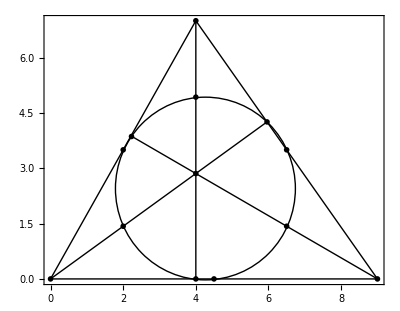

```mathematica
Sketch2D[{pA , pB , pC , tABC,mijAB ,mijAC,mijBC,pbc,pA2,pac,pB2,pab,pC2,cEuler,H,pA3,pB3,pC3} //. {a -> 4, b -> 7, c -> 9}]
```